## Energy and flux definitions

We use Eqs. (C1--C13) of PRD 79, 104023 [http://arxiv.org/abs/0810.5336v1], taking into account various errata on the spin-orbit terms, which can best be found in Eqs. (7.9) and (7.11) of arXiv:0605140v4 [note the version number!].

```mathematica
Energy[0]:=-1/2 ν;
Energy[1]:=0;
Energy[2]:=-3/4-1/12 ν;
Energy[3]:=4/3(2- ν)(χs.Ln)+8/3 δ (χa.Ln);
Energy[4]:=(-27/8+19/8 ν-1/24 ν^2)+ν((χs.χs-χa.χa)-3((χs.Ln)^2-(χa.Ln)^2))+(1/2-ν)((χs.χs)+(χa.χa)-3((χs.Ln)^2+(χa.Ln)^2))+δ(χs.χa-3(χs.Ln)(χa.Ln));
Energy[5]:=(8-(121 ν)/9+(2 ν^2)/9)(χs.Ln)+(8-(31 ν)/9)δ(χa.Ln);
Energy[6]:=-675/64+(34445/576-205/96 π^2)ν-155/96 ν^2-35/5184 ν^3;
Energy[7]:=0;
Unprotect[E];
E[v_]:=Energy[0] v^2(1+∑_(i=2)^6 Energy[i] v^i);
E[v_,Order_]:=Energy[0] v^2(1+∑_(i=2)^Min[Order,6] Energy[i] v^i);
Protect[E];
dEdv[v_]:=-v ν+v^3 ((3 ν)/2+ν^2/6)+v^7 ((675 ν)/16+5/144 (-6889+246 π^2) ν^2+(155 ν^3)/24+(35 ν^4)/1296)+v^4 (10/3 ν^2 χs.Ln-20/3 ν (δ χa.Ln+χs.Ln))+v^6 (-7/9 ν^3 χs.Ln-28 ν (δ χa.Ln+χs.Ln)+7/18 ν^2 (31 δ χa.Ln+121 χs.Ln))+v^5 (ν^3/8+ν^2 (-57/8-18 (χa.Ln)^2+6 χa.χa)+3/8 ν (27-4 χa.χa+12 ((χa.Ln)^2+2 δ χa.Ln χs.Ln+(χs.Ln)^2)-8 δ χs.χa-4 χs.χs));
Flux[0,v_]:=32/5 ν^2;
Flux[1,v_]:=0;
Flux[2,v_]:=-1247/336-35/12 ν;
Flux[3,v_]:=4π+((-11/4+3ν)(χs.Ln)-11/4 δ(χa.Ln));
Flux[4,v_]:=(-44711/9072+9271/504 ν+65/18 ν^2)+(287/96+ν/24)(χs.Ln)^2-(89/96+(7ν)/24)(χs.χs)+(287/96-12ν)(χa.Ln)^2+(-89/96+4ν)(χa.χa)+287/48 δ(χs.Ln)(χa.Ln)-89/48 δ(χs.χa)(*+ν(-103/48(χs.χs-χa.χa)+289/48((χs.Ln)^2-(χa.Ln)^2))*);
Flux[5,v_]:=(-8191/672-583/24 ν)π+(-59/16+(227 ν)/9-(157 ν^2)/9)(χs.Ln)+(-59/16+(701 ν)/36)δ(χa.Ln)-1/4(1-3 ν)(χs.Ln) (1+9 (χa.χa)+3 (χs.χs))-δ/4 (1-ν) (χa.Ln) (1+3 (χa.χa)+9 (χs.χs));
Flux[6,v_]:=(6643739519/69854400+16/3 π^2-1712/105 EulerGamma-856/105 Log[16 v^2])+(-134543/7776+41/48 π^2)ν-94403/3024 ν^2-775/324 ν^3;
Flux[7,v_]:=(-16285/504+214745/1728 ν+193385/3024 ν^2)π;

ℱ[v_]:=Flux[0,v] v^10(1+∑_(i=2)^7 Flux[i,v] v^i);
ℱ[v_,Order_]:=Flux[0,v] v^10(1+∑_(i=2)^Min[Order,7] Flux[i,v] v^i);
Mdot[v_]:=32/5 v^10 ν^2(-1/4 v^5 ((1-ν) δ Subscript[χ, a](1+3 Subscript[χ, a]^2+9 Subscript[χ, s]^2)+(1-3 ν) Subscript[χ, s](1+9 Subscript[χ, a]^2+3 Subscript[χ, s]^2)));
```

## TaylorT1

```mathematica
T1dEdvNum=Simplify[((ℱ[v]+Mdot[v])/(32/5 v^10 ν^2))/.{Ln->{0,0,1},Subscript[χ, a]->0,Subscript[χ, s]->chis,χa->{0,0,0},χs->{0,0,chis},Log[16 v^2]->2ln4v}]/.ν->nu
T1dEdvDen=Simplify[(E'[v]/.{Ln->{0,0,1},χa->{0,0,0},χs->{0,0,chis}})/(-v ν)]/.ν->nu
```

1/209563200(209563200-623700 (1247+980 nu) v^2+52390800 (chis (-11+12 nu)+16 π) v^3-23100 (44711-166878 nu-32760 nu^2+567 chis^2 (-33+4 nu)) v^4+103950 (3024 chis^3 (-1+3 nu)-14 chis (603-3848 nu+2512 nu^2)-3 (8191+16324 nu) π) v^5-(-19931218557+3416878080 EulerGamma+3416878080 ln4v+3625933850 nu+6542127900 nu^2+501270000 nu^3-1117670400 π^2-179001900 nu π^2) v^6+86625 (-78168+300643 nu+154708 nu^2) π v^7)

1-1/6 (9+nu) v^2-10/3 chis (-2+nu) v^3-1/8 (81+24 chis^2-57 nu+nu^2) v^4+7/18 chis (72-121 nu+2 nu^2) v^5-(5 (10935+1674 nu^2+7 nu^3+9 nu (-6889+246 π^2)) v^6)/1296

```mathematica
SetDirectory["/Users/boyle/Research/WaveExtrapolation/Waveforms/PostNewtonian/Notes/"];
OutFile = OpenWrite["OrbitalPhasing_T1.txt"];
dvdtNum2=CForm[SeriesCoefficient[T1dEdvNum,{v,0,2}]];
dvdtNum3=CForm[SeriesCoefficient[T1dEdvNum,{v,0,3}]];
dvdtNum4=CForm[SeriesCoefficient[T1dEdvNum,{v,0,4}]];
dvdtNum5=CForm[SeriesCoefficient[T1dEdvNum,{v,0,5}]];
dvdtNum6=CForm[SeriesCoefficient[T1dEdvNum,{v,0,6}]/.ln4v->0];
dvdtNum6Ln4v=CForm[D[SeriesCoefficient[T1dEdvNum,{v,0,6}],ln4v]];
dvdtNum7=CForm[SeriesCoefficient[T1dEdvNum,{v,0,7}]];
WriteString[OutFile,StringForm["      dvdtNum2(``),\n", dvdtNum2]]
WriteString[OutFile,StringForm["      dvdtNum3(``),\n", dvdtNum3]]
WriteString[OutFile,StringForm["      dvdtNum4(``),\n", dvdtNum4]]
WriteString[OutFile,StringForm["      dvdtNum5(``),\n", dvdtNum5]]
WriteString[OutFile,StringForm["      dvdtNum6(``),\n", dvdtNum6]]
WriteString[OutFile,StringForm["      dvdtNum6Ln4v(``),\n", dvdtNum6Ln4v]]
WriteString[OutFile,StringForm["      dvdtNum7(``),\n", dvdtNum7]]
dvdtDen2=CForm[SeriesCoefficient[T1dEdvDen,{v,0,2}]];
dvdtDen3=CForm[SeriesCoefficient[T1dEdvDen,{v,0,3}]];
dvdtDen4=CForm[SeriesCoefficient[T1dEdvDen,{v,0,4}]];
dvdtDen5=CForm[SeriesCoefficient[T1dEdvDen,{v,0,5}]];
dvdtDen6=CForm[SeriesCoefficient[T1dEdvDen,{v,0,6}]];
WriteString[OutFile,StringForm["      dvdtDen2(``),\n", dvdtDen2]];
WriteString[OutFile,StringForm["      dvdtDen3(``),\n", dvdtDen3]];
WriteString[OutFile,StringForm["      dvdtDen4(``),\n", dvdtDen4]];
WriteString[OutFile,StringForm["      dvdtDen5(``),\n", dvdtDen5]];
WriteString[OutFile,StringForm["      dvdtDen6(``)\n", dvdtDen6]];
Close[OutFile];
```

Stiffness time: -34258.5 (should be less than t1=0.)

The final value of v: 0.504928

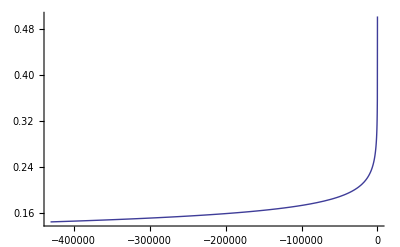

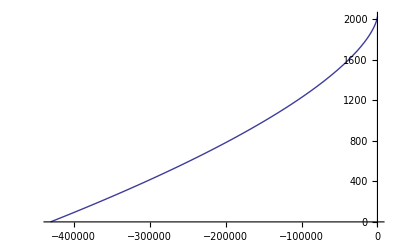

```mathematica
chis=0;
nu=1/4;
v0=0.144;
t0 =- 1.1 5/(256 nu v0^8); (* Guess this, and make sure the stiffness time below is less than t1. *)
t1 = 0.0;
T1dEdv[t_]:=((32/5 v^9 nu T1dEdvNum)/T1dEdvDen/.{ln4v->Log[4v]})/.v->v[t];
Quiet[T1Solution=NDSolve[{v'[t]==T1dEdv[t],v[t0]==v0,Φ'[t]==v[t]^3,Φ[t0]==0},{v,Φ},{t,t0,t1}]];
Print["Stiffness time: ",tOffset = T1Solution[[1,1,2,1,1,2]]," (should be less than t1=", t1, ")"]
Print["The final value of v: ", Evaluate[v[t1+tOffset]/.T1Solution][[1]]]
Plot[Evaluate[v[t+tOffset]/.T1Solution],{t,t0-tOffset,t1},PlotRange->{All,{0,All}}]
Plot[Evaluate[Φ[t+tOffset]/.T1Solution],{t,t0-tOffset,t1},PlotRange->All]
Clear[v0,nu,chis,t0,t1,m1,m2,S1,S2,χ1,χ2,Ln,M,ℳ,δ,χs,χa]
```

## TaylorT2

## TaylorT3

## TaylorT4

```mathematica
T4dEdv=Collect[5/(32ν v^9)Series[Simplify[-(ℱ[v]+Mdot[v])/D[E[v],v]/.{Ln->{0,0,1},Subscript[χ, a]->0,Subscript[χ, s]->chis,χa->{0,0,0},χs->{0,0,chis},Log[16 v^2]->2ln4v}],{v,0,16}],{v,χa,χs,ν},FullSimplify]/.ν->nu
SetDirectory["/Users/boyle/Research/WaveExtrapolation/Waveforms/PostNewtonian/Notes/"];
OutFile = OpenWrite["OrbitalPhasing_T4.txt"];
dvdt2=CForm[SeriesCoefficient[T4dEdv,{v,0,2}]];
dvdt3=CForm[SeriesCoefficient[T4dEdv,{v,0,3}]];
dvdt4=CForm[SeriesCoefficient[T4dEdv,{v,0,4}]];
dvdt5=CForm[SeriesCoefficient[T4dEdv,{v,0,5}]];
dvdt6=CForm[SeriesCoefficient[T4dEdv,{v,0,6}]/.ln4v->0];
dvdt6Ln4v=CForm[D[SeriesCoefficient[T4dEdv,{v,0,6}],ln4v]];
dvdt7=CForm[SeriesCoefficient[T4dEdv,{v,0,7}]];
WriteString[OutFile,StringForm["      dvdt2(``),\n", dvdt2]]
WriteString[OutFile,StringForm["      dvdt3(``),\n", dvdt3]]
WriteString[OutFile,StringForm["      dvdt4(``),\n", dvdt4]]
WriteString[OutFile,StringForm["      dvdt5(``),\n", dvdt5]]
WriteString[OutFile,StringForm["      dvdt6(``),\n", dvdt6]]
WriteString[OutFile,StringForm["      dvdt6Ln4v(``),\n", dvdt6Ln4v]]
WriteString[OutFile,StringForm["      dvdt7(``)\n", dvdt7]]
Close[OutFile];
```

1+(-743/336-(11 nu)/4) v^2+(-(113 chis)/12+(19 chis nu)/3+4 π) v^3+(34103/18144+(81 chis^2)/16+(13661/2016-chis^2/4) nu+(59 nu^2)/18) v^4+(-(79 chis nu^2)/3+(-63646 chis-3024 chis^3-12477 π)/2016+nu ((23353 chis)/252+(9 chis^3)/2-(189 π)/8)) v^5+(16447322263/139708800+(128495 chis^2)/2016-(1712 EulerGamma)/105-(1712 ln4v)/105+(541/896+(1517 chis^2)/72) nu^2-(5605 nu^3)/2592-(80 chis π)/3+(16 π^2)/3+nu (-56198689/217728-(23441 chis^2)/288+(40 chis π)/3+(451 π^2)/48)) v^6+(-(2539613 chis)/27216-(257 chis^3)/4+(2045 chis nu^3)/216-(4415 π)/4032+12 chis^2 π+(nu^2 (-1193295 chis-504 chis^3+365980 π))/6048+(nu (10831889 chis+2397276 chis^3+3228075 π))/54432) v^7